Swerve Drive Robot Simulator - FRC Team 1072

```mathematica
(*Rotation around the origin*)
rotationmatrix[θ_] ={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};

(*getOriginalWheelPts=Function[
{point},
{point+{-0.1,0.23},point+{0.1,0.23},point+{0.1,-0.23},point+{-0.1,-0.23},point+{-0.1,0.23}}
];*)

(*2D Transformation Functions*)
getWheelPts=Function[
{point,θ},
Module[
{pts={{-0.1,0.23},{0.1,0.23},{0.1,-0.23},{-0.1,-0.23},{-0.1,0.23}}},
rotate[pts,θ]+{point,point,point,point,point}
]
];

rotate = Function[
{pts, θ},
Table[
pts[[i]].rotationmatrix[θ],
{i,1,5}
]
];

(*Vector Functions*)
scaleRotation[rotVec_,x_,rotMag_]=rotVec*(x/rotMag); 

(*Checks for indeterminate values in angle calculations*)
checkIfDefined = Function[
{val},
If[(SameQ[val,Indeterminate]),0,val]
];

(*Surpress errors handled in function above *)
Off[Power::infy]
Off[Infinity::indet]
Off[ArcTan::indet]
```

```mathematica
Manipulate[
Module[
{
robot = Graphics[{FaceForm[],EdgeForm[Black],Rectangle[{-robotWidth/2,-robotLength/2},{robotWidth/2,robotLength/2}]},PlotLabel-> Column[{Style["Legend:",Black,FontSize->16],Style["Translation Vectors",Red],Style["Rotation Vectors",Blue],Style["Net Vectors",Purple],"Rotation Circle"},Center],AxesOrigin->{{0,0},{0,0}},PlotRange->{{-4,4},{-2.5,3}},Axes->False],
robotVectorOrigin={0,4},
topLeftPoint ={-robotWidth/2+0.3, robotLength/2 - 0.3},
topRightPoint ={robotWidth/2 - 0.3,  robotLength/2 - 0.3},
bottomLeftPoint ={-robotWidth/2+0.3, -robotLength/2 + 0.3},
bottomRightPoint ={robotWidth/2-0.3, -robotLength/2 + 0.3},
wheelToCenterDistance = Sqrt[(robotWidth/2 - 0.3)^2+  (robotLength/2 - 0.3)^2],
translation = {leftJoystickX,leftJoystickY},
rotationMagnitude=Sqrt[robotWidth^2+robotLength^2],
topLeftRotation={robotLength,robotWidth},
topRightRotation = {robotLength,-robotWidth},
bottomLeftRotation={-robotLength,robotWidth},
bottomRightRotation = {-robotLength,-robotWidth},
θTopLeft =checkIfDefined[Pi/2+ArcTan[
({leftJoystickX,leftJoystickY} + scaleRotation[{robotLength,robotWidth},rightJoystickX,Sqrt[robotWidth^2+robotLength^2]])[[1]],({leftJoystickX,leftJoystickY} + scaleRotation[{robotLength,robotWidth},rightJoystickX,Sqrt[robotWidth^2+robotLength^2]])[[2]]
]
],(*Module doesn't let you use local vars, so everything that was just defined has to be wrote out the long way :( *)
θTopRight =checkIfDefined[Pi/2+ArcTan[
({leftJoystickX,leftJoystickY} + scaleRotation[{robotLength,-robotWidth},rightJoystickX,Sqrt[robotWidth^2+robotLength^2]])[[1]],({leftJoystickX,leftJoystickY} + scaleRotation[{robotLength,-robotWidth},rightJoystickX,Sqrt[robotWidth^2+robotLength^2]])[[2]]
]
],
θBottomLeft =checkIfDefined[Pi/2+ArcTan[
({leftJoystickX,leftJoystickY} + scaleRotation[{-robotLength,robotWidth},rightJoystickX,Sqrt[robotWidth^2+robotLength^2]])[[1]],
({leftJoystickX,leftJoystickY} + scaleRotation[{-robotLength,robotWidth},rightJoystickX,Sqrt[robotWidth^2+robotLength^2]])[[2]]
]
],
θBottomRight =checkIfDefined[Pi/2+ArcTan[
({leftJoystickX,leftJoystickY} + scaleRotation[{-robotLength,-robotWidth},rightJoystickX,Sqrt[robotWidth^2+robotLength^2]])[[1]],
({leftJoystickX,leftJoystickY} + scaleRotation[{-robotLength,-robotWidth},rightJoystickX,Sqrt[robotWidth^2+robotLength^2]])[[2]]
]
]
},
Show[
robot,
ListPlot[{topLeftPoint,topRightPoint,bottomLeftPoint,bottomRightPoint},PlotStyle->{Black}],
Graphics[{Opacity[0.3],Circle[{0,0},wheelToCenterDistance]}],
ListPlot[getWheelPts[topLeftPoint,θTopLeft],Joined->True,PlotStyle->Opacity[0.75]],
ListPlot[getWheelPts[topRightPoint,θTopRight],Joined->True,PlotStyle->Opacity[0.75]],
ListPlot[getWheelPts[bottomLeftPoint,θBottomLeft],Joined->True,PlotStyle->Opacity[0.75]],
ListPlot[getWheelPts[bottomRightPoint,θBottomRight],Joined->True,PlotStyle->Opacity[0.75]],
Graphics[{Red,Arrow[{topLeftPoint,topLeftPoint+translation}]}],
Graphics[{Red,Arrow[{topRightPoint,topRightPoint+translation}]}],
Graphics[{Red,Arrow[{bottomLeftPoint,bottomLeftPoint+translation}]}],
Graphics[{Red,Arrow[{bottomRightPoint,bottomRightPoint+translation}]}],
Graphics[{Blue,Arrow[{topLeftPoint,topLeftPoint+scaleRotation[topLeftRotation,rightJoystickX,rotationMagnitude]}]}],
Graphics[{Blue,Arrow[{topRightPoint,topRightPoint+scaleRotation[topRightRotation,rightJoystickX,rotationMagnitude]}]}],
Graphics[{Blue,Arrow[{bottomLeftPoint,bottomLeftPoint+scaleRotation[bottomLeftRotation,rightJoystickX,rotationMagnitude]}]}],
Graphics[{Blue,Arrow[{bottomRightPoint,bottomRightPoint+scaleRotation[bottomRightRotation,rightJoystickX,rotationMagnitude]}]}],
Graphics[{Purple,Arrow[{topLeftPoint,topLeftPoint+translation+scaleRotation[topLeftRotation,rightJoystickX,rotationMagnitude]}]}],
Graphics[{Purple,Arrow[{topRightPoint,topRightPoint+translation+scaleRotation[topRightRotation,rightJoystickX,rotationMagnitude]}]}],
Graphics[{Purple,Arrow[{bottomLeftPoint,bottomLeftPoint+translation+scaleRotation[bottomLeftRotation,rightJoystickX,rotationMagnitude]}]}],
Graphics[{Purple,Arrow[{bottomRightPoint,bottomRightPoint+translation+scaleRotation[bottomRightRotation,rightJoystickX,rotationMagnitude]}]}]
]
],
{{robotWidth,2,"Robot Width"},1.5,4},{{robotLength,3,"Robot Length"},1.5,4},{{leftJoystickY,0,"Up/Down Translation"},-1,1},{{leftJoystickX,0,"Left/Right Translation"},-1,1},{{rightJoystickX,0,"Rotation"},-1,1},
SaveDefinitions->True
]
```

Simulates a robot with a swerve drivetrain (https://team1640.com/wiki/index.php/Swerve_Central). Given a combination of robot translation and rotation values, the translation, rotation, and output vectors for each of the four independent swerve modules are calculated and displayed. This demonstration is useful to understand how to calculate the vectors for each module such that the robot will translate and rotate as desired. Note: An output vector represents a velocity vector, where the direction of the vector is the direction that the module should point and the magnitude of the vector is proportional to how fast the module's wheel should rotate (the maximum output vector magnitude is Sqrt[2] and the minimum is 0, so the output vector must be scaled to attain the desired range).

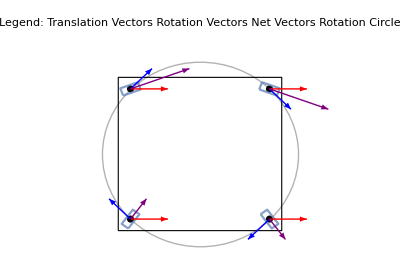

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

robot

robotics

drive

drivetrain

swerve

swerve module

FRC

first

first robotics competition

Contributed by: Jatin Kohli